# Maps and periodic orbits.

Just a few reminders. A map is a function
	g:ℝ^m→ℝ^m
An orbit of a map with initial condition x_0 is the sequence
	x_0,x_1=g[x_0],…,x_(k+1)=g[x_k],… 
An orbit is periodic if there is a p≥1 satisfying
	x_(k+p)=x_k for all k.
The period of a periodic orbit is the smallest p≥1 that works.

## First Return Maps of ODEs on Sections are Maps

The first return map for the Roseller ODE on the plane y_2==0 is a map on the 2D plane 
	S_2=span((1
0
0),(0
0
1))  
Periodic orbits for the Rosseler ODE with winding number w are periodic maps with period p=w on the plane S_2.

## Rosseller Peak Map

The peak height of the loops on the Rosseler map is a 1D map on the line -∞<x<∞.

```mathematica
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
IVP[y0_] := {y'[t]==f[StdParams][y[t]],y[0]==y0};
IVPJ[y0_]:={
y'[t]==f[StdParams][y[t]],y[0]==y0,
J'[t]==df[StdParams][y[t]].J[t],J[0]==IdentityMatrix[3]}
```

Here is the peak height map computation

```mathematica
y0={3.2,8.4,7.6}; TMax=12345; NumPoints=10^3;
yData=ConstantArray[0,{NumPoints,3}]; i=0; tEnd=TMax;
ySol=NDSolveValue[IVP[y0],y,{t,0, TMax},
Method->{"EventLocator", "Event":>y'[t]⟦3⟧==0,"Direction"->-1,
"EventAction":>If[i++<NumPoints,
yData⟦i⟧=y[t],(tEnd=t;"StopIntegration")]}];

ODEPic=ParametricPlot3D[ySol[t],{t,0,tEnd},
PlotRange->All,PlotPoints->10^3,PlotStyle->Thin,ColorFunction->Function[{x,y,z,t},Hue[t]]];
DotPic =ListPointPlot3D[yData,PlotStyle->Black];
TabView[{
"ODE"->ODEPic,
"Peaks"->Show[ODEPic, DotPic],
"z vs i"->ListPlot[yData⟦All,3⟧,PlotRange->All,AxesLabel->{"i","z"}],
"z_(i - 1) vs z_i"->ListPlot[{yData⟦1;;-2,3⟧,yData⟦2;;-1,3⟧}ᵀ,PlotRange->All,AxesLabel->{"z_(i - 1)","z_i"},Prolog->Line[{{0,0},{20,20}}]],
"z_(i - 2) vs z_i"->ListPlot[{yData⟦1;;-3,3⟧,yData⟦3;;-1,3⟧}ᵀ,PlotRange->All,AxesLabel->{"z_(i - 2)","z_i"},Prolog->Line[{{0,0},{20,20}}]]
},4]
```

12345

It turns out the steep hump in the map is fundamental to the complexity of a map!

## Simple 1D Maps: Logistic Map

Lets make the simplest 1D map that looks like our “peak” map.   The scaled quadratic
	g_r[x]=r x (1-x)
r is a parameter and x is the input and output is called the logistic map.  Lets get a feel for what happens to the orbits as we play with r and x_0.

```mathematica
MaxIter=12356;
r=3.55;
x=0.43;
Data=Table[x=r x (1-x),{MaxIter}];
Data=Data⟦2000;;-1⟧;
TabView[{
"i vs x"->ListPlot[Data,PlotRange->All,Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"x_(i - 1) vs x_i"->ListPlot[{Data⟦1;;-2⟧,Data⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},ColorFunction->Function[{i,x},Hue[0.9i]],
PlotStyle->PointSize[0.01]]
}]
```

12

Here is a uniform sample of x values going at the same time for different values of r.

```mathematica
n=50;Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];
TabView[
Table[
Data=NestList[r#(1-#)&,xs,32];
r->ListPlot[Dataᵀ,PlotStyle->PointSize[0.008],PlotRange->All,Frame->True,FrameLabel->{"k","x"}],
{r,3.0,4.0,0.05}],4
]
```

123456789101112131415161718192021

It would be nice to see a bunch of different “r” maps evolving at the same time.

```mathematica
n=50;Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];
Steps=6;
{rMin,rMax,Δr}={2.5,4.0,0.01};
rxData=Flatten[Table[{r,xs⟦j⟧},{r,rMin,rMax,Δr},{j,n}],1];
g[{r_,x_}]:={r,r x * (1-x)}
k=0;
ListAnimate[Table[
Pic=ListPlot[rxData,Frame->True,FrameLabel->{"r","x"},GridLines->Automatic,PlotLabel->StringForm["k=``",k++]];
rxData=Map[g,rxData];
Pic,
{100}]]
```

Since you don’t really care how it got there it is common to just take a lot of steps.  You can resolve more detail by using more points!

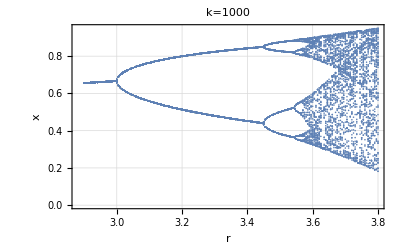

```mathematica
n=100;Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];
Steps=6;
{rMin,rMax,Δr}={2.9,3.8,0.005};
rxData=Flatten[Table[{r,xs⟦j⟧},{r,rMin,rMax,Δr},{j,n}],1];
g[{r_,x_}]:={r,r x * (1-x)}
k=0;
Do[k++;
rxData=Map[g,rxData],
{1000}]
ListPlot[rxData,Frame->True,FrameLabel->{"r","x"},GridLines->Automatic,PlotLabel->StringForm["k=``",k]]
```

## Simple 1D Maps: Tent Map

An even simpler (in some sense) 1D map that looks like our “peak” map is the piecewise linear
	g_μ[x]=μ min(x,1-x)
μ is a parameter and x is the input and output is called the tent map.  Only in the crudest sense do the look similar!

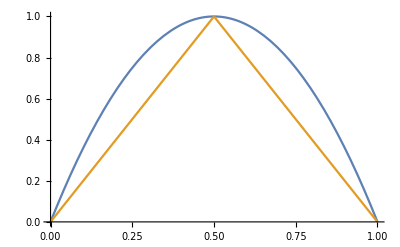

```mathematica
μ=2;r=4;
Plot[ {r x (1-x), μ Min[x,1-x]},{x,0,1}]
```

Lets get a feel for what happens to the orbits.

```mathematica
MaxIter=1234;
μ=1.05;
x=0.43;
Data=Table[x=μ Min[ x ,1-x],{MaxIter}];
EndData=Drop[Data,Floor[MaxIter/2]];
TabView[{
"i vs x"->ListPlot[Data,PlotRange->All,Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"i vs x (end)"->ListPlot[EndData,PlotRange->All,Ticks->{None,Automatic},Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"x_(i - 1) vs x_i"->ListPlot[{Data⟦1;;-2⟧,Data⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},ColorFunction->Function[{i,x},Hue[0.9i]],
PlotStyle->PointSize[0.01]],
"x_(i - 1) vs x_i (end)"->ListPlot[{EndData⟦1;;-2⟧,EndData⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},
PlotStyle->PointSize[0.01]]
}]
```

1234

Lets look at the bifurcation diagram.

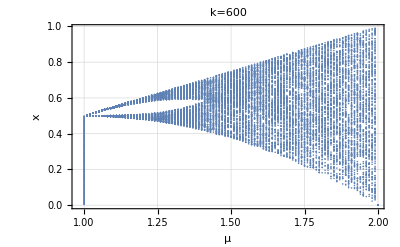

```mathematica
n=200;Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];
{μMin,μMax,Δμ}={1.0,2.0,0.01};
μxData=Flatten[Table[{μ,xs⟦j⟧},{μ,μMin,μMax,Δμ},{j,n}],1];
Steps=600;
g[{μ_,x_}]:={μ,μ Min[x, 1-x]}
Do[μxData=Map[g,μxData],
{Steps}]
ListPlot[μxData,Frame->True,FrameLabel->{"μ","x"},GridLines->Automatic,PlotLabel->StringForm["k=``",Steps]]
```

## Simple 1D Maps: Other Maps

I am going to make another “hump” function and see what it looks like

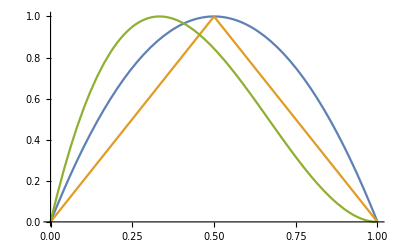

```mathematica
μ=2;r=4;s=27/4;
Plot[ {r x (1-x), μ Min[x,1-x], s x (1-x)^2},{x,0,1}]
```

Lets get a feel for what happens to the orbits.

```mathematica
MaxIter=1234;
s=5.1
x=0.43;
Data=Table[x=s x (1-x)^2,{MaxIter}];
EndData=Drop[Data,Floor[MaxIter/2]];
TabView[{
"i vs x"->ListPlot[Data,PlotRange->All,Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"i vs x (end)"->ListPlot[EndData,PlotRange->All,Ticks->{None,Automatic},Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"x_(i - 1) vs x_i"->ListPlot[{Data⟦1;;-2⟧,Data⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},ColorFunction->Function[{i,x},Hue[0.9i]],
PlotStyle->PointSize[0.01]],
"x_(i - 1) vs x_i (end)"->ListPlot[{EndData⟦1;;-2⟧,EndData⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},
PlotStyle->PointSize[0.01]]
}]
```

5.1

1234

Lets look at the bifurcation diagram.

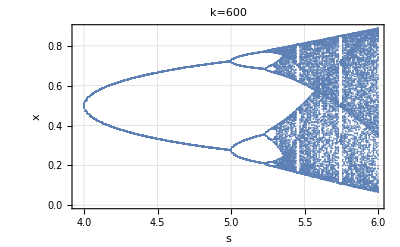

```mathematica
n=200;Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];
{sMin,sMax,Δs}={4.0,6.0,0.01};
sxData=Flatten[Table[{s,xs⟦j⟧},{s,sMin,sMax,Δs},{j,n}],1];
Steps=600;
g[{s_,x_}]:={s,s x (1-x)^2}
Do[sxData=Map[g,sxData],
{Steps}]
ListPlot[sxData,Frame->True,FrameLabel->{"s","x"},GridLines->Automatic,PlotLabel->StringForm["k=``",Steps]]
```

It looks as though we should see period 8 just a smidge above s=5.25

```mathematica
MaxIter=1234;
s=5.28
x=0.43;
Data=Table[x=s x (1-x)^2,{MaxIter}];
EndData=Drop[Data,Floor[MaxIter/2]];
TabView[{
"i vs x"->ListPlot[Data,PlotRange->All,Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"i vs x (end)"->ListPlot[EndData,PlotRange->All,Ticks->{None,Automatic},Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"x_(i - 1) vs x_i"->ListPlot[{Data⟦1;;-2⟧,Data⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},ColorFunction->Function[{i,x},Hue[0.9i]],
PlotStyle->PointSize[0.01]],
"x_(i - 1) vs x_i (end)"->ListPlot[{EndData⟦1;;-2⟧,EndData⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},
PlotStyle->PointSize[0.01]]
}]
```

5.28

1234

## Analytics for The Logistic Map: x←r x (1-x)

A fixed point x=g[x] gives a constant orbit.  There are two for every r!

```mathematica
Clear[r,x]
g[r_][x_]:=r x (1-x)
Solve[g[r][x]==x,x]
```

{{x→0},{x→(-1+r)/r}}

The simplest periodic orbit is 
	x_2 | = | g[x_1]
x_1 | = | g[x_2]
If you combine them you have
	x_1 | = | g[g[x_1]]
x_2 | = | g[g[x_2]]
point x=g[x] gives a constant orbit.  The equation is 
	r^2 (1-x) x (1-r (1-x) x)=x
or expanding 
	r^2 x-r^2 x^2-r^3 x^2+2 r^3 x^3-r^3 x^4=x
and it is not surprising that there are 4 roots of the quartic.  The four roots are below

```mathematica
Clear[r,x]
g[r_][x_]:=r x (1-x)
Solve[g[r][g[r][x]]==x,x]
```

{{x→0},{x→(-1+r)/r},{x→(r+r^2-r √(-3-2 r+r^2))/(2 r^2)},{x→(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}}

All 4 roots are real if -3-2 r+r^2=(r-3)(r+1)≥0.  This is the bifurcation point

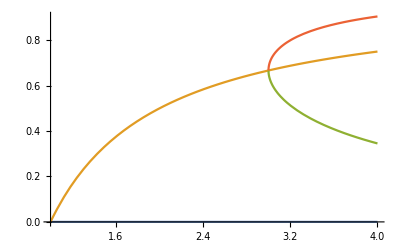

```mathematica
Plot[ {0,(-1+r)/r,(r+r^2-r √(-3-2 r+r^2))/(2 r^2),(r+r^2+r √(-3-2 r+r^2))/(2 r^2)},{r, 1,4}]
```

The pattern is a little different for period 3

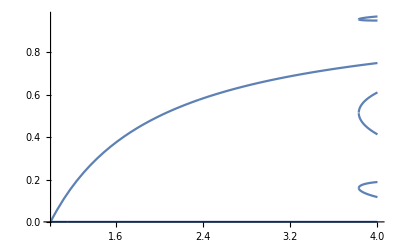

```mathematica
Clear[r,x]
g[r_][x_]:=r x (1-x)
Plot[x/.Solve[g[r][g[r][g[r][x]]]==x,x],{r,1,4}]
```

The pattern returns to the familiar one for period 4

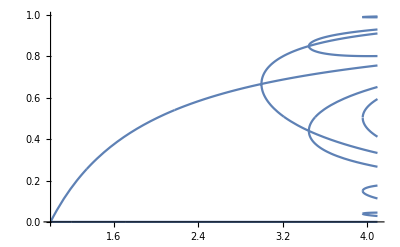

```mathematica
Clear[r,x]
g[r_][x_]:=r x (1-x)
Plot[x/.Solve[g[r][g[r][g[r][g[r][x]]]]==x,x],{r,1,4.1}]
```